```mathematica
NN = 3
```

3

```mathematica
maxr = 100
CMSz[a_] := Exp[1/NN Log[a]]/Exp[1/NN Log[-(1 - a)]]∑_(r=1)^maxr NN/(r NN + 1)( 1 - 1/(1 - a))^r
CMSzsimple[a_] := Exp[1/NN Log[a]]/Exp[1/NN ⅈ π] a
CMSzsimple1[a_] := Exp[1/NN Log[a]]/Exp[1/NN Log[-(1 - a)]] a
CMSN[a_] := Exp[1/NN Log[a]]/Exp[1/NN Log[-(1 - a)]] Log [  1 - a  ] + ⅈ 0
CMSNN[ξ_] := Exp[1/NN Log[1/2 + ⅈ ξ]]/Exp[1/NN Log[-1/2 + ⅈ ξ]] Log[ 1/2 - ⅈ ξ ]
```

100

```mathematica
m0[a_] := ⅇ^(1/NN Log[a])
σ0[a_] := ⅇ^(1/NN Log[ 1 + a])

mj[a_] := m0[a] ⅇ^(2 π ⅈ j / NN)
σ1[a_] := σ0[a]  ⅇ^((2 π ⅈ)/NN)
CMS[a_] := (NN σ0[a] ( ⅇ^((2 π ⅈ)/NN) - 1) + ∑_(j=0)^(NN-1) mj[a] ( Log[ σ1[a] - mj[a] ] - Log [ σ0[a] - mj[a] ] ))/(m0[a] ( ⅇ^((2 π ⅈ)/NN) - 1))
CMSE[a_] :=  (NN σ0[a] ( ⅇ^((2 π ⅈ)/NN) - 1) + ∑_(j=0)^(NN-1) mj[a] ( Log[ 1 - mj[a]/σ1[a] ] - Log [ 1 - mj[a]/σ0[a] ] ))/(m0[a] ( ⅇ^((2 π ⅈ)/NN) - 1))
```

```mathematica
MM= 400;
XY  = Table[{Null, Null}, {MM}];
XY1  = Table[{Null, Null}, {MM}];
XYgen  = Table[{Null, Null}, {MM}];
XYE  = Table[{Null, Null}, {MM}];
XYN  = Table[{Null, Null}, {MM}];
XYα = Table[{Null, Null}, {MM}];

centre = 180;
width = 60;
For [ j = 0, j < MM, j++, 
ϕ = π/180(centre - width/2+ (width j)/MM);

a0 = 1.0 ⅇ^(ⅈ ϕ);
 z = a /. FindRoot[ { Re[CMSzsimple[a]] == 0 }, {a, a0}];
XY[[j+1]] = { -1 +Re[z], Im[z] };

a01 = 0.5 ⅇ^(ⅈ ϕ);
z1 = a /. FindRoot[ { Re[CMSz[a]] == 0 }, {a, a01}];
XY1[[j+1]] = { -1 +Re[z1], Im[z1] };

a0gen = 2.0 ⅇ^(ⅈ ϕ);
zgen = a /. FindRoot[ { Re[CMS[a]] == 0 }, {a, a0gen}];
XYgen[[j+1]] = { Re[zgen], Im[zgen] };

a0E = 2.0 ⅇ^(ⅈ ϕ);
zE = a /. FindRoot[ { Re[CMSE[a]] == 0 }, {a, a0E}];
XYE[[j+1]] = { Re[zE], Im[zE] };

a0N = 1.5 ⅇ^(ⅈ ϕ);
zN = a /. FindRoot[ { Re[CMSN[a]] == 0 }, {a, a0N}];
XYN[[j+1]] = { -1 + Re[zN], Im[zN] };

α0 = 0.9 ⅇ^(ⅈ ϕ);
zα = α /. FindRoot[ {  Re[Exp[1/NN Log[α]] Log [ 1 - α] ] == 0 }, {α, α0} ];
XYα[[j+1]] = { Re[zα], Im[zα] };
 ];
```

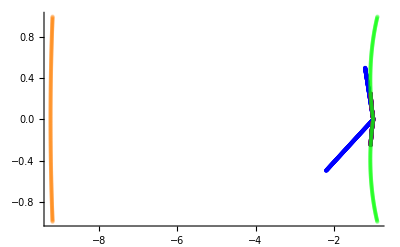

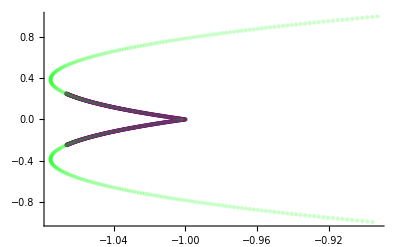

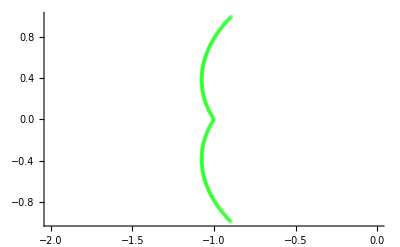

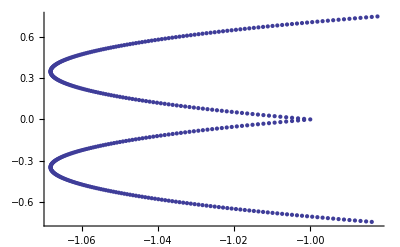

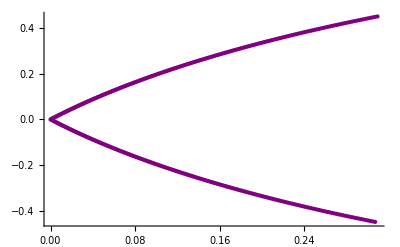

```mathematica
ListPlot[   {XY,XY1,XYgen,XYE},PlotStyle->{Blue,Purple,Directive[Opacity[0.2,Green],PointSize[Small]], Orange}   ]
ListPlot[   {XY1,XYgen},PlotStyle->{Purple,Directive[Opacity[0.2,Green], PointSize[Small]]}   ]
ListPlot[   {XYgen}, PlotStyle->{Directive[Opacity[0.2,Green],PointSize[Small]]} , PlotRange->{{-2.,0},Automatic}  ]
ListPlot[   {XYN},PlotStyle->{Thick} ]
ListPlot[   {XYα}, PlotStyle->{Directive[Thick, Purple]} ]
```